## Author Informations

#### Authors: A. C. Lehum, Huan Souza Date: 18/05/2021 Filiation: Universidade Federal do Pará Emails: lehum@ufpa.br, huan.souza@icen.ufpa.br

# Electrodynamics coupled to linearized gravity

#### Preliminaries

```mathematica
Quit[]
```

```mathematica
description="Electrodynamics coupled to linearized gravity";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts","FeynHelpers"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
FAPatch[PatchModelsOnly->True];
$KeepLogDivergentScalelessIntegrals=True;
MakeBoxes[mu,TraditionalForm]:="μ";
MakeBoxes[nu,TraditionalForm]:="ν";
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
MakeBoxes[m1,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(1\)]\)";
MakeBoxes[m2,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(2\)]\)";
ScalarProduct[p,p]=p^2
```

p^2

#### 1-loop γ self-energy

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}],Model->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4}];
seph1=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields1]&)[top1[1,1]];
```

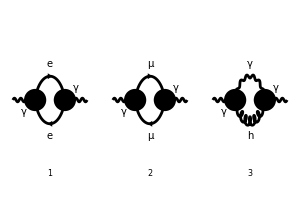

```mathematica
Paint[seph1,ColumnsXRows->{3,2},SheetHeader->{"Photon self-energy"},Numbering->Simple,ImageSize->{300,200}];
```

```mathematica
AbsoluteTiming[For[
i=1,i≤3,i++,{
Pamp[i]=DiagramExtract[seph1,i],
Pamp1[i]=FCFAConvert[CreateFeynAmp[Pamp[i],Truncated->True,GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ},UndoChiralSplittings->True]//DotExpand//Simplify//Expand,
Pamp2[i]=TID[Pamp1[i],k,ToPaVe->True]//DiracSimplify//Simplify,
Pamp3[i]=PaXEvaluate[Pamp2[i],$FCAdvice=False],
Pamp4[i]=Coefficient[Pamp3[i],1/Epsilon]*1/Epsilon//Expand//Factor}
];]
```

{13.1555,Null}

```mathematica
photon[1]=Sum[Pamp4[i],{i,1,3}]//DotExpand//Simplify//Expand//Factor
```

-((p^2 g^μν-p^μ p^ν) (16 e^2-2 κ^2 p^2+3 κ^2 p^2 ξ_(T(1))))/(96 π^2 ε)

#### 1-loop electron self-energy

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}],Model->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4}];
sepsi1=(InsertFields[#1,{F[1]}->{F[1]},Sequence@@fields1]&)[top1[1,1]];
```

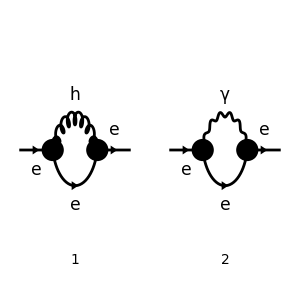

```mathematica
Paint[sepsi1,ColumnsXRows->{2,1},SheetHeader->{"Electron self-energy"},Numbering->Simple,ImageSize->{300,300}];
```

```mathematica
AbsoluteTiming[For[
i=1,i≤2,i++,{
Famp[i]=DiagramExtract[sepsi1,i],
Famp1[i]=FCFAConvert[CreateFeynAmp[Famp[i],Truncated->True,GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ},UndoChiralSplittings->True]//DotExpand//Simplify//Expand,
Famp2[i]=TID[Famp1[i],k,ToPaVe->True]//DiracSimplify//Simplify,
Famp3[i]=PaXEvaluate[Famp2[i],$FCAdvice=False],
Famp4[i]=Coefficient[Famp3[i],1/Epsilon]*1/Epsilon//Expand//Factor}
];]
```

{4.10579,Null}

```mathematica
fermion[1]=Sum[Famp4[i],{i,1,2}]//DotExpand//Simplify//Expand//Factor
```

1/(512 π^2 ε)(32 e^2 ξ_(V(1)) γ·p-32 e^2 m_1 ξ_(V(1))-96 e^2 m_1-19 κ^2 p^2 γ·p+36 κ^2 p^2 m_1-24 κ^2 p^2 m_1 ξ_(T(1))+15 κ^2 p^2 ξ_(T(1)) γ·p+37 κ^2 m_1^2 γ·p-29 κ^2 m_1^2 ξ_(T(1)) γ·p-46 κ^2 m_1^3+38 κ^2 m_1^3 ξ_(T(1)))

```mathematica
fermionHO[1]=Coefficient[fermion[1],p^2]*p^2//Simplify//Expand//Simplify
```

(κ^2 p^2 ((15 ξ_(T(1))-19) γ·p+12 m_1 (3-2 ξ_(T(1)))))/(512 π^2 ε)

The divergence fermionHO[1] is absorbed by a high order counterterm.

```mathematica
fermionDirac[1]=fermion[1]/.{p^2->0}//Simplify
```

(γ·p (32 e^2 ξ_(V(1))+37 κ^2 m_1^2-29 κ^2 m_1^2 ξ_(T(1)))-32 e^2 m_1 (ξ_(V(1))+3)-46 κ^2 m_1^3+38 κ^2 m_1^3 ξ_(T(1)))/(512 π^2 ε)

```mathematica
wf1=Coefficient[fermionDirac[1],DiracGamma[Momentum[p,D],D]]//Expand
```

(e^2 ξ_(V(1)))/(16 π^2 ε)+(37 κ^2 m_1^2)/(512 π^2 ε)-(29 κ^2 m_1^2 ξ_(T(1)))/(512 π^2 ε)

```mathematica
mass1=fermionDirac[1]/.{DiracGamma[Momentum[p,D],D]->0}//Expand
```

-(3 e^2 m_1)/(16 π^2 ε)-(e^2 m_1 ξ_(V(1)))/(16 π^2 ε)-(23 κ^2 m_1^3)/(256 π^2 ε)+(19 κ^2 m_1^3 ξ_(T(1)))/(256 π^2 ε)

The term fermionDirac[1] is the UV divergent correction to Dirac Lagrangian.  The muon self-energy is obtained by the replacement of F[1]  to F[2] in the sepsi1 function.

#### 1-loop vertex correction

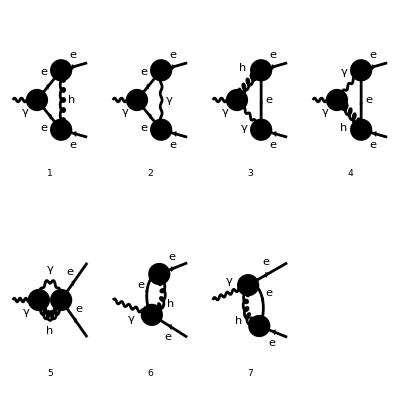

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}],Model->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
vertex1=(InsertFields[#1,{V[1]}->{F[1],-F[1]},Sequence@@fields1]&)[top1[1,2]];
Paint[vertex1,ColumnsXRows->{4,2},SheetHeader->{"Vertex correction"},Numbering->Simple,ImageSize->{400,400}];
```

```mathematica
AbsoluteTiming[For[
i=1,i≤7,i++,{
amp[i]=DiagramExtract[vertex1,i],
amp1[i]=FCFAConvert[CreateFeynAmp[amp[i],Truncated->True,GaugeRules->{}],IncomingMomenta->{0},OutgoingMomenta->{0,0},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ},UndoChiralSplittings->True]//DotExpand//Simplify//Expand,
amp2[i]=TID[amp1[i],k,ToPaVe->True]//DiracSimplify,
amp3[i]=PaXEvaluateUVIRSplit[amp2[i],$FCAdvice=False],
amp4[i]=Coefficient[amp3[i],1/EpsilonUV]*1/Epsilon//Expand//Factor}
];]
```

{4.86561,Null}

The computation of the first order in the external small momenta expansion (i.e. Γ^μ(p=q=l=0))  results

```mathematica
vertex1l[1]=Sum[amp4[i],{i,1,7}]//DotExpand//Simplify//Expand
```

-(e^3 γ^μ ξ_(V(1)))/(16 π^2 ε)-(37 e κ^2 m_1^2 γ^μ)/(512 π^2 ε)+(29 e κ^2 m_1^2 γ^μ ξ_(T(1)))/(512 π^2 ε)

where vertex1l[1] is the UV divergent part of the vertex1 amplitude that is absorbed by the counterterm Z_1. All UV divergences depending on external momenta will be absorbed by high order counterterms. 
In addition, the vertex interaction involving muons is obtained by the replacement of F[1] to F[2] in the vertex1 function.